```mathematica
l:=0.3;
```

```mathematica
alpha := 30.0;
```

```mathematica
vel:=0.1;
```

```mathematica
A:={0.0,0.0};
```

```mathematica
T:={0.0,l};
```

```mathematica
XA[t_]:=A[[1]]+t*vel*Sin[alpha*Degree+phi[t]*Degree]
```

```mathematica
YA[t_]:=A[[2]]+t*vel*Cos[alpha*Degree+phi[t]*Degree]
```

```mathematica
phi[t_]:=180-2*ArcCos[t*vel*Sin[alpha*Degree]/2/l]/Degree
```

```mathematica
XO[t_]:=T[[1]]+t*vel*Cos[alpha]*Sin[phi[t]*Degree]
```

```mathematica
YO[t_]:=T[[2]]+t*vel*Cos[alpha]*Cos[phi[t]*Degree]
```

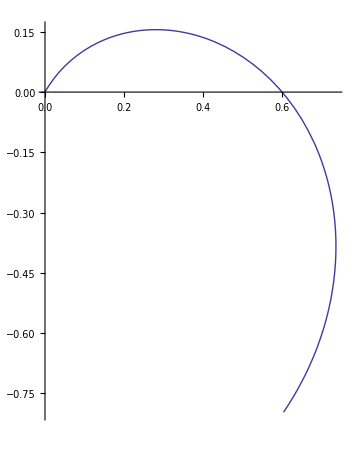

```mathematica
ParametricPlot[{XA[t],YA[t]},{t,0,10}]
```

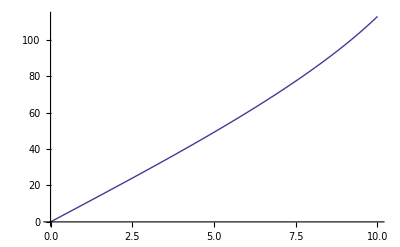

```mathematica
Plot[phi[t],{t,0,10}]
```

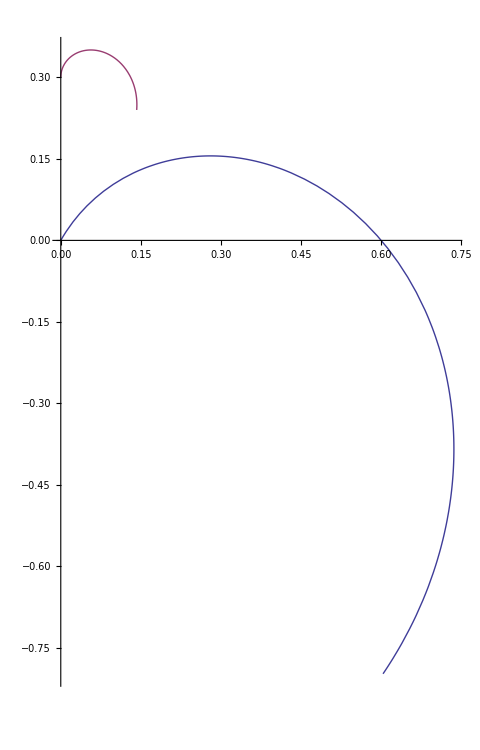

```mathematica
ParametricPlot[{{XA[t],YA[t]},{XO[t],YO[t]}},{t,0,10}]
```